## 3. Domača naloga

Najprej napišemo kapacieteno matriko omrežja. V vsako polje matrike vpišemo 2 podatka: minimalni pretok in maksimalni pretok.

```mathematica
A={{{0,0}, {2,4}, {2,4}, {10,18}, {8,18}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}}, {{0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {6,8}, {0,0}, {0,0}, {0,0}, {0,0}}, {{0,0}, {4,6}, {0,0}, {0,0}, {0,0}, {0,0}, {4,10}, {0,0}, {0,0}, {0,0}}, {{0,0}, {0,0}, {2,6}, {0,0}, {0,0}, {0,0}, {0,0}, {4,6}, {0,0}, {0,0}}, {{0,0}, {0,0}, {0,0}, {0,6}, {0,0}, {0,0}, {0,0}, {0,0}, {6,8}, {0,0}}, {{0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {11,16}}, {{0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {4,5}, {0,0}, {0,0}, {0,0}, {4,6}}, {{0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {6,6}, {0,0}, {0,0}, {4,6}}, {{0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {2,6}, {0,0}, {4,10}}, {{0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}}};
```

Sedaj iz matrike razberemo povezave v grafu. Uporabimo funkcijo s predavanj.

```mathematica
povezave={};minKapacitete={};maxKapacitete={};
n=Length[A];
Do[If[A[[i,j]]≠{0,0},
(AppendTo[povezave,i->j];
AppendTo[minKapacitete,First[A[[i,j]]]];
AppendTo[maxKapacitete,Last[A[[i,j]]]])],{i,n},{j,n}]
povezave
minKapacitete
maxKapacitete
vozlisca=Table[i,{i,n}];
```

{1->2,1->3,1->4,1->5,2->6,3->2,3->7,4->3,4->8,5->4,5->9,6->10,7->6,7->10,8->7,8->10,9->8,9->10}

{2,2,10,8,6,4,4,2,4,0,6,11,4,4,6,4,2,4}

{4,4,18,18,8,6,10,6,6,6,8,16,5,6,6,6,6,10}

Sedaj lahko graf sestavimo skupaj in narišemo.

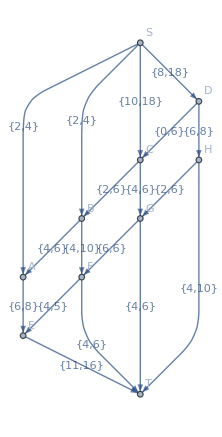

```mathematica
G=Graph[vozlisca,povezave,
EdgeCapacity->maxKapacitete,
EdgeLabels->Table[povezave[[i]]->{minKapacitete[[i]],maxKapacitete[[i]]},{i,Length[povezave]}],
VertexLabels->{1->"S",2->"A",3->"B",4->"C",5->"D",6->"E",7->"F",8->"G",9->"H",10->"T"}]
```

Sedaj poiščemo največji možen pretok.

```mathematica
F=FindMaximumFlow[G,1,10,"OptimumFlowData"];
```

```mathematica
F["FlowValue"]
```

28

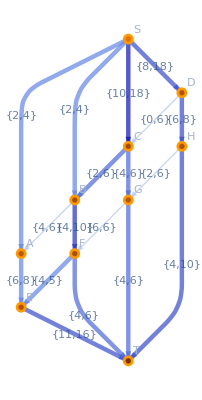

```mathematica
F["FlowGraph"]
```

```mathematica
F["FlowMatrix"]//MatrixForm
Grid[{#,F[#]}&/@F["EdgeList"],Frame->All,Alignment->Left]
```

(0 | 4 | 4 | 12 | 8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0
0 | 0 | 6 | 0 | 0 | 0 | 0 | 6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

1->2 | 4
1->3 | 4
1->4 | 12
1->5 | 8
2->6 | 4
3->7 | 10
4->3 | 6
4->8 | 6
5->9 | 8
6->10 | 8
7->6 | 4
7->10 | 6
8->10 | 6
9->10 | 8

Problem je, ker še nismo upoštevali minimalnega obveznega pretoka.